```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY193_cloudy/sec_int_data/610nm.dat"]
```

{{1.46129,0.172271},{1.36603,0.219055},{1.32759,0.233252},{1.2815,0.239411},{1.23231,0.247016},{1.21009,0.263517},{1.18279,0.242083},{1.15809,0.203267},{1.13892,0.159991},{1.12738,0.144533},{1.09219,0.192107},{1.09146,0.239411},{1.09503,0.298993},{1.10053,0.30822},{1.1079,0.306528},{1.12128,0.305645},{1.13179,0.287282},{1.14273,0.296245},{1.16583,0.293937},{1.1846,0.291475},{1.20387,0.327071},{1.22314,0.291774},{1.24682,0.285555}}

0.431594-0.14887 x

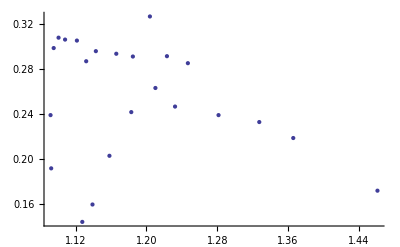

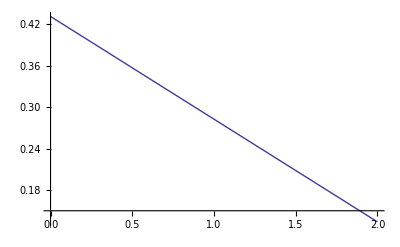

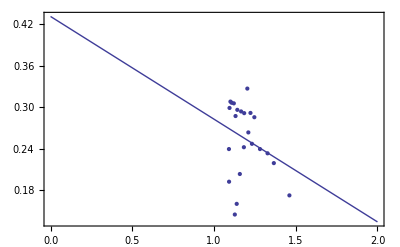

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```